--- Initializing Advanced Combinatorial Logic Tree ---

--- Generating Master MHG Permutation Tree ---

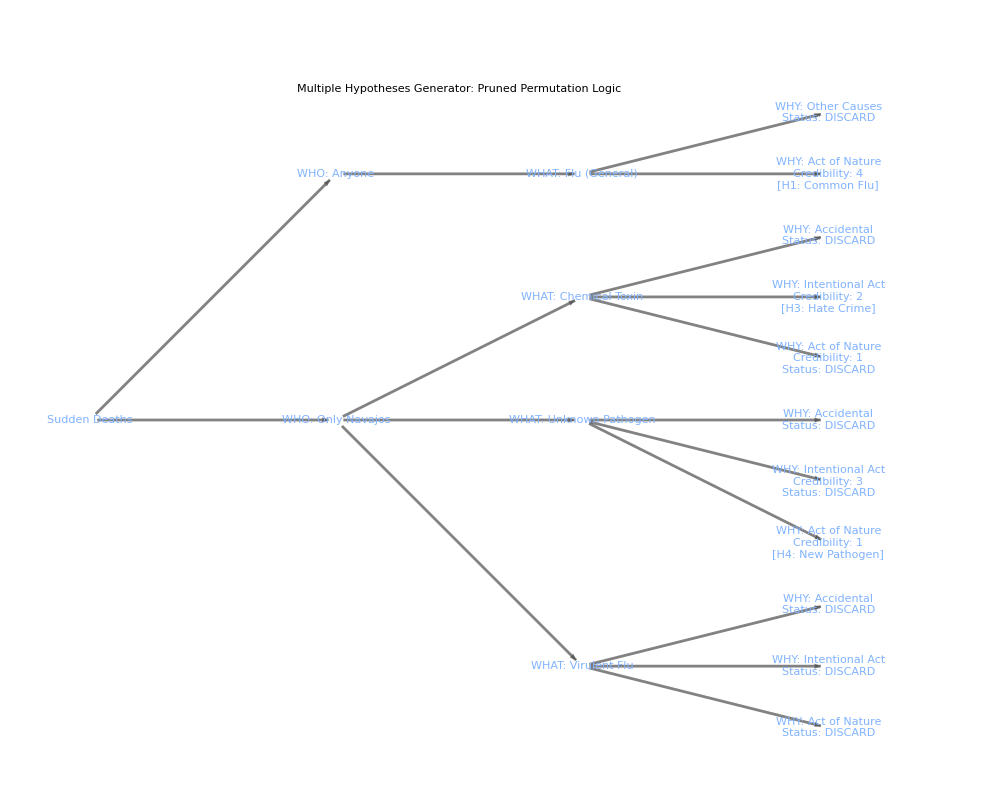

✅ MASTER MHG TREE COMPLETE. Graph exported to Vault.

```mathematica
(* ======================================================*)(*01.5:Hypothesis Generation-THE ULTIMATE MHG TREE*)(* ======================================================*)Print["--- Initializing Advanced Combinatorial Logic Tree ---"];

edges={"Sudden Deaths"->"WHO: Isolated Demographic\n(Navajos Only)","Sudden Deaths"->"WHO: General Population\n(Indiscriminate)","WHO: Isolated Demographic\n(Navajos Only)"->"WHAT: Virulent Flu","WHO: Isolated Demographic\n(Navajos Only)"->"WHAT: Unknown Pathogen","WHO: Isolated Demographic\n(Navajos Only)"->"WHAT: Chemical Toxin","WHAT: Virulent Flu"->"WHY: Act of Nature\n(Flu Discarded)","WHAT: Virulent Flu"->"WHY: Intentional Act\n(Flu Discarded)","WHAT: Virulent Flu"->"WHY: Accidental\n(Flu Discarded)","WHAT: Unknown Pathogen"->"WHY: Act of Nature\nCredibility: 1\n[H4: New Pathogen]","WHAT: Unknown Pathogen"->"WHY: Intentional Act\nCredibility: 3\n(Pathogen Discarded)","WHAT: Unknown Pathogen"->"WHY: Accidental\n(Pathogen Discarded)","WHAT: Chemical Toxin"->"WHY: Act of Nature\nCredibility: 1\n(Toxin Discarded)","WHAT: Chemical Toxin"->"WHY: Intentional Act\nCredibility: 2\n[H3: Hate Crime]","WHAT: Chemical Toxin"->"WHY: Accidental\n(Toxin Discarded)","WHO: General Population\n(Indiscriminate)"->"WHAT: Flu (General)","WHAT: Flu (General)"->"WHY: Act of Nature\nCredibility: 4\n[H1: Common Flu]","WHAT: Flu (General)"->"WHY: Other Causes\n(Other Discarded)"};

ClearAll[nodeAesthetic];
nodeAesthetic[name_String]:=Module[{bgColor,fontColor,borderColor,textToDisplay},textToDisplay=StringReplace[name,{"(Flu Discarded)"->"Status: DISCARD","(Pathogen Discarded)"->"Status: DISCARD","(Toxin Discarded)"->"Status: DISCARD","(Other Discarded)"->"Status: DISCARD"}];
Which[StringContainsQ[name,"[H"],bgColor=Lighter[Blue,0.9];fontColor=Darker[Blue,0.4];borderColor=Lighter[Blue,0.4];,StringContainsQ[name,"DISCARD"]||StringContainsQ[name,"Discarded"],bgColor=GrayLevel[0.96];fontColor=GrayLevel[0.6];borderColor=GrayLevel[0.9];,StringContainsQ[name,"Sudden Deaths"],bgColor=GrayLevel[0.15];fontColor=White;borderColor=Black;,True,bgColor=White;fontColor=Black;borderColor=GrayLevel[0.7];];
Framed[Style[textToDisplay,10,FontFamily->"Helvetica",Bold,FontColor->fontColor,TextAlignment->Center],Background->bgColor,FrameStyle->Directive[Thickness[0.003],borderColor],RoundingRadius->6,FrameMargins->10]];

Print["\n--- Generating Master MHG Permutation Tree ---"];
treePlot=Graph[edges,VertexShapeFunction->(Inset[nodeAesthetic[#2],#1]&),EdgeStyle->Directive[Darker[Gray,0.4],AbsoluteThickness[2]],GraphLayout->{"LayeredDigraphEmbedding","RootVertex"->"Sudden Deaths","Orientation"->Left},ImageSize->{1000,800},PlotLabel->Style["Multiple Hypotheses Generator: Pruned Permutation Logic",Bold,16,FontFamily->"Helvetica"]];

Export["/Users/Western/Desktop/ThesisCode/Vault/Permutation_Tree_Master.pdf",treePlot];
Print["✅ MASTER MHG TREE COMPLETE. Graph exported to Vault."];

(*---EXPORT TARGET HYPOTHESES FOR THE MATRIX---*)
finalHypotheses={"H1: Common Flu","H2: Toxic Substance","H3: Hate Crime","H4: New Pathogen"};
Export["/Users/Western/Desktop/ThesisCode/Vault/target_hypotheses.md",StringJoin[Riffle[finalHypotheses,"\n"]],"Text"];
Print["✅ Target Hypotheses perfectly stored in Vault."];
```